## Cannabis Brownie Kinetics

### CBDA →^k1 CBD →^k2 THC THCA →^k3 THC →^k4 CBN or A →^k1 B →^k2 D C →^k3 D →^k4 E

Estimated initial 9.1 mM CBDA + 1.1 mM THCA averaged from various strains
Assumed decarboxylation (k1 & k3) and degradation (k2 & k4) reactions are elementary and follow the Arrhenius equation with constants below

```mathematica
Grid[{
{"Rate Constant","A [s^-1]","E_a [kJ/mol]"},
{"k1",1.9*^12,112},
{"k2",9.5*^2,52},
{"k3",1.0*^9,86},
{"k4",1.2*^6,77}
}
,Frame->All]
```

Rate Constant | A [s^-1] | E_a [kJ/mol]
k1 | 1.9×10^12 | 112
k2 | 950. | 52
k3 | 1.×10^9 | 86
k4 | 1.2×10^6 | 77

```mathematica
ca0=9.1; (*mM CBDA*)
cb0=0; (*mM CBD*)
cc0=1.1; (*mM THCA*)
cd0=0; (*mM THC*)
ce0=0; (*mM CBN*)

cacstr:=ca0/(1+60t k1cstr);
cbcstr:=(cb0+60t k1cstr cacstr)/(1+60t k2cstr);
cccstr:=cc0/(1+60t k3cstr);
cdcstr:=(cd0+60t k2cstr cbcstr+60t k3cstr cccstr)/(1+60t k4cstr);
cecstr:=ca0+cb0+cc0+cd0+ce0-cacstr-cbcstr-cccstr-cdcstr;

ca0new:=ca0/(1+60taucstr k1cstr);
cb0new:=(cb0+60taucstr k1cstr ca0new)/(1+60taucstr k2cstr);
cc0new:=cc0/(1+60taucstr k3cstr);
cd0new:=(cd0+60taucstr k2cstr cb0new+60taucstr k3cstr cc0new)/(1+60taucstr k4cstr);
ce0new:=ca0+cb0+cc0+cd0+ce0-ca0new-cb0new-cc0new-cd0new;

capfr:=ca0new Exp[-60(t-taucstr) k1pfr];
cbpfr:=k1pfr/(k2pfr-k1pfr)capfr+(cb0new(k2pfr-k1pfr)-k1pfr ca0new)/(k2pfr-k1pfr)Exp[-60(t-taucstr) k2pfr];
ccpfr:=cc0new Exp[-60(t-taucstr) k3pfr];
	vara:=(k1pfr k2pfr ca0new)/(k2pfr-k1pfr);
	varb:=(k2pfr(cb0new(k2pfr-k1pfr)-k1pfr ca0new))/(k2pfr-k1pfr);
	varc:=k3pfr cc0new;
cdpfr:=1/(k4pfr-k1pfr)vara (Exp[-60(t-taucstr) k1pfr]-Exp[-60(t-taucstr) k4pfr])+1/(k4pfr-k2pfr)varb (Exp[-60(t-taucstr) k2pfr]-Exp[-60(t-taucstr) k4pfr])+1/(k4pfr-k3pfr)varc (Exp[-60(t-taucstr) k3pfr]-Exp[-60(t-taucstr) k4pfr])+cd0new Exp[-60(t-taucstr)k4pfr];
cepfr:=ca0+cb0+cc0+cd0+ce0-capfr-cbpfr-ccpfr-cdpfr;

k1cstr:=1.9*10^12 Exp[-112/(8.314*10^-3(tempcstr+459.67)/(9/5))];
k2cstr:=9.5*10^2 Exp[-52/(8.314*10^-3(tempcstr+459.67)/(9/5))];
k3cstr:=1.0*10^9 Exp[-86/(8.314*10^-3(tempcstr+459.67)/(9/5))];
k4cstr:=1.2*10^6 Exp[-77/(8.314*10^-3(tempcstr+459.67)/(9/5))];
k1pfr:=1.9*10^12 Exp[-112/(8.314*10^-3(temppfr+459.67)/(9/5))];
k2pfr:=9.5*10^2 Exp[-52/(8.314*10^-3(temppfr+459.67)/(9/5))];
k3pfr:=1.0*10^9 Exp[-86/(8.314*10^-3(temppfr+459.67)/(9/5))];
k4pfr:=1.2*10^6 Exp[-77/(8.314*10^-3(temppfr+459.67)/(9/5))];

p[t_,left_,right_]:=HeavisideTheta[t-left] HeavisideTheta[right-t];
line1:=Line[{{taucstr,0},{taucstr,ca0+cb0+cc0+cd0+ce0}}];
line2:=Line[{{taucstr+taupfr,0},{taucstr+taupfr,ca0+cb0+cc0+cd0+ce0}}];

Manipulate[
tempcstr;
temppfr;
Plot[{
cacstr p[t,0,taucstr],
cbcstr p[t,0,taucstr],
cccstr p[t,0,taucstr],
cdcstr p[t,0,taucstr],
cecstr p[t,0,taucstr],
capfr p[t,taucstr,taucstr+taupfr],
cbpfr p[t,taucstr,taucstr+taupfr],
ccpfr p[t,taucstr,taucstr+taupfr],
cdpfr p[t,taucstr,taucstr+taupfr],
cepfr p[t,taucstr,taucstr+taupfr]
},{t,0,taucstr+taupfr},
Epilog-> {line1,line2},
PlotStyle-> {Red,Orange, Yellow,Green,Blue},
PlotLabel-> "Series CSTR + PFR Concentrations",
AxesLabel-> {"Time [min]","Concentration [mM]"},
PlotLegends-> {"CBDA","CBD","THCA","THC","CBN"},
PlotRange-> {0,ca0+cb0+cc0+cd0+ce0}],
{{tempcstr,240,"CSTR Temp [oF]"},70,500,Appearance-> "Labeled"},
{{taucstr,30,"CSTR τ [min]"},0,5000,Appearance-> "Labeled"},
{{temppfr,300,"PFR Temp [oF]"},70,500,Appearance-> "Labeled"},
{{taupfr,30,"PFR τ [min]"},0,5000,Appearance-> "Labeled"},
LocalizeVariables->False]
```

Setting PFR time and temp to recipe-specific 22 min and 212 oF, CSTR time and temp can be optimized for final THC concentration

```mathematica
ca0=9.1; (*mM CBDA*)
cb0=0; (*mM CBD*)
cc0=1.1; (*mM THCA*)
cd0=0; (*mM THC*)
ce0=0; (*mM CBN*)

ca0new:=ca0/(1+60taucstr k1cstr);
cb0new:=(cb0+60taucstr k1cstr ca0new)/(1+60taucstr k2cstr);
cc0new:=cc0/(1+60taucstr k3cstr);
cd0new:=(cd0+60taucstr k2cstr cb0new+60taucstr k3cstr cc0new)/(1+60taucstr k4cstr);
ce0new:=ca0+cb0+cc0+cd0+ce0-ca0new-cb0new-cc0new-cd0new;

capfr:=ca0new Exp[-60taupfr k1pfr];
cbpfr:=k1pfr/(k2pfr-k1pfr)capfr+(cb0new(k2pfr-k1pfr)-k1pfr ca0new)/(k2pfr-k1pfr)Exp[-60taupfr k2pfr];
ccpfr:=cc0new Exp[-60taupfr k3pfr];
	vara:=(k1pfr k2pfr ca0new)/(k2pfr-k1pfr);
	varb:=(k2pfr(cb0new(k2pfr-k1pfr)-k1pfr ca0new))/(k2pfr-k1pfr);
	varc:=k3pfr cc0new;
cdpfr:=(vara (Exp[-60taupfr k1pfr]-Exp[-60taupfr k4pfr]))/(k4pfr-k1pfr)+(varb (Exp[-60taupfr k2pfr]-Exp[-60taupfr k4pfr]))/(k4pfr-k2pfr)+(varc (Exp[-60taupfr k3pfr]-Exp[-60taupfr k4pfr]))/(k4pfr-k3pfr)+cd0new Exp[-60taupfr k4pfr];
cepfr:=ca0+cb0+cc0+cd0+ce0-capfr-cbpfr-ccpfr-cdpfr;

k1cstr:=1.9*10^12 Exp[-112/(8.314*10^-3(tempcstr+459.67)/(9/5))];
k2cstr:=9.5*10^2 Exp[-52/(8.314*10^-3(tempcstr+459.67)/(9/5))];
k3cstr:=1.0*10^9 Exp[-86/(8.314*10^-3(tempcstr+459.67)/(9/5))];
k4cstr:=1.2*10^6 Exp[-77/(8.314*10^-3(tempcstr+459.67)/(9/5))];
k1pfr:=1.9*10^12 Exp[-112/(8.314*10^-3(temppfr+459.67)/(9/5))];
k2pfr:=9.5*10^2 Exp[-52/(8.314*10^-3(temppfr+459.67)/(9/5))];
k3pfr:=1.0*10^9 Exp[-86/(8.314*10^-3(temppfr+459.67)/(9/5))];
k4pfr:=1.2*10^6 Exp[-77/(8.314*10^-3(temppfr+459.67)/(9/5))];

temppfr=212;
taupfr=22;

Plot3D[{cdpfr(*,4.05*)},
{taucstr,0,20000},{tempcstr,100,250},
PlotRange->Automatic,
AxesLabel-> {"CSTR Time [min]","CSTR Temp [oF]","THC [mM]"},
PlotLabel-> "THC after CSTR + PFR",
ColorFunction-> ColorData["TemperatureMap"],
Mesh->All]
```

-Graphics3D-

### Optimization

CSTR time [min] and temp [oF] could not be optimized for CBD because concentration diverged with infinite temp for 0 time.
THC concentration is maximized at 0.264232 mM (post-16x dilution in the PFR) for time [min] and temp [oF] below

{3182.09,163.718}

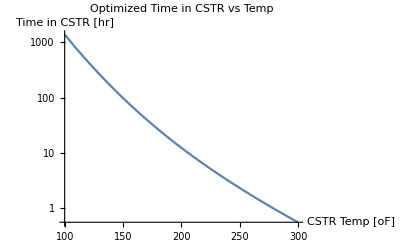

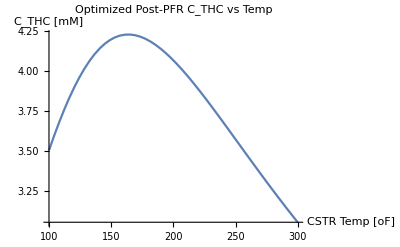

```mathematica
ca0=9.1; (*mM CBDA*)
cb0=0; (*CBD*)
cc0=1.1; (*mM THCA*)
cd0=0; (*THC*)
ce0=0; (*CBN*)

(*k1cstr:=1.9*10^12 Exp[-112/(8.314*10^-3(tempcstr+459.67)/(9/5))];
k2cstr:=9.5*10^2 Exp[-52/(8.314*10^-3(tempcstr+459.67)/(9/5))];
k3cstr:=1.0*10^9 Exp[-86/(8.314*10^-3(tempcstr+459.67)/(9/5))];
k4cstr:=1.2*10^6 Exp[-77/(8.314*10^-3(tempcstr+459.67)/(9/5))];*)

k1cstrop:=1.9*10^12 Exp[-112/(8.314*10^-3(tempcstrop+459.67)/(9/5))];
k2cstrop:=9.5*10^2 Exp[-52/(8.314*10^-3(tempcstrop+459.67)/(9/5))];
k3cstrop:=1.0*10^9 Exp[-86/(8.314*10^-3(tempcstrop+459.67)/(9/5))];
k4cstrop:=1.2*10^6 Exp[-77/(8.314*10^-3(tempcstrop+459.67)/(9/5))];
k1pfr:=1.9*10^12 Exp[-112/(8.314*10^-3(temppfr+459.67)/(9/5))];
k2pfr:=9.5*10^2 Exp[-52/(8.314*10^-3(temppfr+459.67)/(9/5))];
k3pfr:=1.0*10^9 Exp[-86/(8.314*10^-3(temppfr+459.67)/(9/5))];
k4pfr:=1.2*10^6 Exp[-77/(8.314*10^-3(temppfr+459.67)/(9/5))];

ca0new:=ca0/(1+60taucstrop k1cstrop);
cb0new:=(cb0+60taucstrop k1cstrop ca0new)/(1+60taucstrop k2cstrop);
cc0new:=cc0/(1+60taucstrop k3cstrop);
cd0new:=(cd0+60taucstrop k2cstrop cb0new+60taucstrop k3cstrop cc0new)/(1+60taucstrop k4cstrop);
ce0new:=ca0+cb0+cc0+cd0+ce0-ca0new-cb0new-cc0new-cd0new;

ca0newmax:=ca0/(1+60taucstrmax k1cstrop);
cb0newmax:=(cb0+60taucstrmax k1cstrop ca0newmax)/(1+60taucstrmax k2cstrop);
cc0newmax:=cc0/(1+60taucstrmax k3cstrop);
cd0newmax:=(cd0+60taucstrmax k2cstrop cb0newmax+60taucstrmax k3cstrop cc0newmax)/(1+60taucstrmax k4cstrop);
ce0newmax:=ca0+cb0+cc0+cd0+ce0-ca0newmax-cb0newmax-cc0newmax-cd0newmax;

temppfr=212;
taupfr=22;

capfr:=ca0new Exp[-60taupfr k1pfr];
cbpfr:=k1pfr/(k2pfr-k1pfr)capfr+(cb0new(k2pfr-k1pfr)-k1pfr ca0new)/(k2pfr-k1pfr)Exp[-60taupfr k2pfr];
ccpfr:=cc0new Exp[-60taupfr k3pfr];
	vara:=(k1pfr k2pfr ca0new)/(k2pfr-k1pfr);
	varb:=(k2pfr(cb0new(k2pfr-k1pfr)-k1pfr ca0new))/(k2pfr-k1pfr);
	varc:=k3pfr cc0new;
cdpfr:=1/(k4pfr-k1pfr)vara (Exp[-60taupfr k1pfr]-Exp[-60taupfr k4pfr])+1/(k4pfr-k2pfr)varb (Exp[-60taupfr k2pfr]-Exp[-60taupfr k4pfr])+1/(k4pfr-k3pfr)varc (Exp[-60taupfr k3pfr]-Exp[-60taupfr k4pfr])+cd0new Exp[-60taupfr k4pfr];
cepfr:=ca0+cb0+cc0+cd0+ce0-capfr-cbpfr-ccpfr-cdpfr;

capfrmax:=ca0newmax Exp[-60taupfr k1pfr];
cbpfrmax:=k1pfr/(k2pfr-k1pfr)capfrmax+(cb0newmax(k2pfr-k1pfr)-k1pfr ca0newmax)/(k2pfr-k1pfr)Exp[-60taupfr k2pfr];
ccpfrmax:=cc0newmax Exp[-60taupfr k3pfr];
	varamax:=(k1pfr k2pfr ca0newmax)/(k2pfr-k1pfr);
	varbmax:=(k2pfr(cb0newmax(k2pfr-k1pfr)-k1pfr ca0newmax))/(k2pfr-k1pfr);
	varcmax:=k3pfr cc0newmax;
cdpfrmax:=1/(k4pfr-k1pfr)varamax (Exp[-60taupfr k1pfr]-Exp[-60taupfr k4pfr])+1/(k4pfr-k2pfr)varbmax (Exp[-60taupfr k2pfr]-Exp[-60taupfr k4pfr])+1/(k4pfr-k3pfr)varcmax (Exp[-60taupfr k3pfr]-Exp[-60taupfr k4pfr])+cd0newmax Exp[-60taupfr k4pfr];
cepfrmax:=ca0+cb0+cc0+cd0+ce0-capfrmax-cbpfrmax-ccpfrmax-cdpfrmax;

(*4.2277190685 mM before dilution*)
NArgMax[{cdpfr,taucstrop≥ 0,tempcstrop≥ 0},{taucstrop,tempcstrop}]

taucstrmax:=NArgMax[{cdpfr,taucstrop≥ 0},taucstrop];

LogPlot[taucstrmax/60,
{tempcstrop,100,300},
PlotLabel->"Optimized Time in CSTR vs Temp",
AxesLabel->{"CSTR Temp [oF]","Time in CSTR [hr]"},
MaxRecursion->0]

Plot[cdpfrmax,
{tempcstrop,100,300},
PlotRange->All,
PlotLabel->"Optimized Post-PFR C_THC vs Temp",
AxesLabel->{"CSTR Temp [oF]","C_THC [mM]"},
MaxRecursion->0]
```

### Final Concentrations (Diluted 16x)

```mathematica
Grid[{
{"Compound","CBDA","CBD","THCA","THC","CBN"},
{"Label","CA","CB","CC","CD","CE"},
{"Initial Conc [mM]",9.1,0,1.1,0,0},
{"Final Conc [mM]",0.989/16,2.619/16,0.0159/16,4.227/16,2.349/16}
}
,Frame->All]
```

Compound | CBDA | CBD | THCA | THC | CBN
Label | CA | CB | CC | CD | CE
Initial Conc [mM] | 9.1 | 0 | 1.1 | 0 | 0
Final Conc [mM] | 0.0618125 | 0.163688 | 0.00099375 | 0.264188 | 0.146813

### Reactor Calculations

THC = 4.227719069 mM at 163.72 oF for 3182 min ≈ 53 hr ≈ 2.2 days
CBD concentration max at ∞ temp for 0 time

13x9x1 in^3 pan has a surface area to volume ratio of 2.376
A pipe matching this would have diameter 3.025 in
For 1 in thick brownies to be produced every 1 s, volumetric flow rate would be π*(3.025/2)^2 1 = 7.187 in^3/s = 424 L/hr
Including the 16x dilution from CSTR to PFR, 26.5 L oil/hr required
424 L/hr brownie mix * 22 min = 155.467 L = 9487 in^3
PFR length = V/(π(D/2)^2) = 1320 in = 110 ft long PFR

1 oz cannabis / 13*9*1 in^3 batch = 1.74 g / brownie

26.5 L/hr for 53 hrs → 1404 L CSTR

Reactor calculations hidden above

Batch SA/V ratio = 2.376
Match PFR → 3” diam
1” thick brownie per second (1.75 g ea) → 424 L/hr
22 min → 155 L PFR (110’ long)

16x dilution → 27 L/hr
2.2 days → 1400 L CSTR
THC = 4.2 mM at 163.72 oF

Wholesale $1400 / lb
14 lb / hr
Costs $20,000 / hr
Sold for $20 ea → $72,000 / hr revenue

### Expenditure

Prices
	1 oz cannabis / 0.5 cup vegetable oil = 14 lbs cannabis + 26.5 L vegetable oil / hr
	Wholesale $1400 / lb
		$20,000 / hr for cannabis
	$0.06 / fl oz vegetable oil
		$54 / hr for oil
	brownie mix + 2 eggs + 0.25 cup water = 16.3 brownies
	$0.10 / egg = $0.02 / brownie
	$2 / brownie mix box = $0.13 / brownie
		$468 / hr for mix
		$72 / hr for eggs
		
		~$20,000 / hr total
		$20 / brownie = $72,000 / hr

```mathematica
PieChart[{20000,468, 72, 54},
ChartLegends-> {"Cannabis","Brownie Mix", "Eggs", "Vegetable Oil"}]
```

-Graphics-

### Cannabis Curve

```mathematica
r:=(1+0.9Cos[8θ])(1+0.1Cos[24θ])(0.9+0.1Cos[200θ])(1+Sin[θ]);
Animate[
PolarPlot[r,{θ,0,2π},
Axes->False,
ColorFunction->Function[{x,y,t,r},Hue[r+color]],
ColorFunctionScaling->False,
MaxRecursion->5,
PlotRange->All],
{color,0,4},
AnimationRunning->False]
```